```mathematica
4*3+16*2+64
```

108

```mathematica
5*4+16*3
```

```mathematica
∑_(i=1)^n (i)*n^i
```

```mathematica
Table[(n (1-n^n-n^(1+n)+n^(2+n)))/(-1+n)^2,{n,3,10}]
```

{102,1252,18555,324726,6565468,150652552,3868151445,109876543210}

```mathematica
Table[-(n (1-n+n^2-n^n))/(-1+n)^2,{n,3,10}]
```

{15,108,970,11190,160125,2739128,54480996,1234567890}

```mathematica
Table[∑_(i=1)^(n^2) i/n,{n,3,10}]
```

{15,34,65,111,175,260,369,505}

```mathematica
Map[SquareQ[Abs[Det[Partition[#,3]]]]&,Permutations[Range[9]]]
```

{True,True,True,True,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,«362825»,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,True,True,True,True}

```mathematica
Tally[%]
```

{{True,26424},{False,336456}}

```mathematica
Map[SquarePQ[Abs[Det[Partition[#,3]]]]&,Permutations[Range[9]]]
```

{True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,«362826»,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,True,True,True,True}

```mathematica
Tally[%]
```

{{True,11304},{False,351576}}

```mathematica
SquareQ[x_]:=IntegerQ[√x]
```

```mathematica
SquarePQ[16]
```

False

```mathematica
SquarePQ[x_]:=IntegerQ[√x]&&Divisible[x,5]
```

```mathematica
c={0,0};
```

```mathematica
Monitor[Do[c=Block[{m=Partition[Permute[Range[25],RandomPermutation[25]],5]},Block[{d=Abs[Det[m]]},Piecewise[{{Piecewise[{{c, !SquarePQ[d]}, {{d,m}, SquarePQ[d]}}], d>First[c]}, {c, d≤First[c]}}]]],{i,1000000}],{c,i}]
```

```mathematica
c
```

{3496900,{{3,19,15,25,14},{9,24,1,7,22},{5,11,23,4,17},{16,10,21,6,8},{12,2,13,20,18}}}

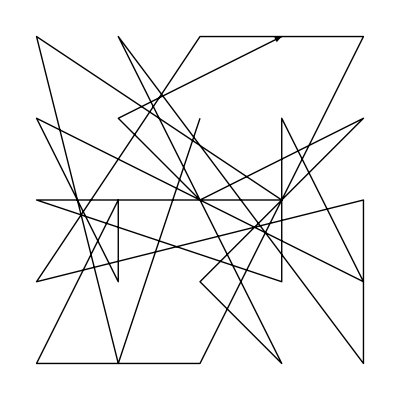
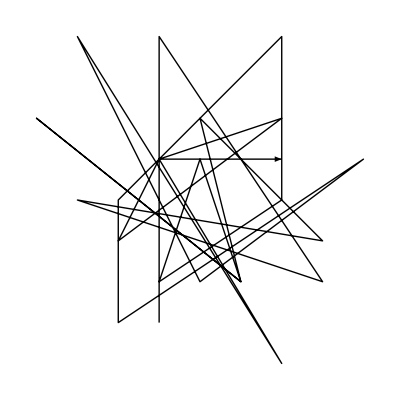
{(3 | 19 | 15 | 25 | 14
9 | 24 | 1 | 7 | 22
5 | 11 | 23 | 4 | 17
16 | 10 | 21 | 6 | 8
12 | 2 | 13 | 20 | 18),{-Graphics-,{{-1,-3},{-1,4},{3,-2},{-3,0},{3,-1},{0,2},{1,-2},{-4,2},{1,-2},{0,1},{-1,-2},{2,0},{2,4},{-2,0},{-2,-3},{4,1},{0,-2},{-3,4},{2,-4},{-1,1},{2,2},{-2,-1},{-1,1},{2,1}},-Graphics-}}

```mathematica
GM[{{3,19,15,25,14},{9,24,1,7,22},{5,11,23,4,17},{16,10,21,6,8},{12,2,13,20,18}}]
```

```mathematica
FactorInteger[3496900]
```

{{2,2},{5,2},{11,2},{17,2}}

```mathematica
{32400,{{8,3,9,15},{10,4,12,2},{16,14,6,7},{1,13,11,5}}}
```

```mathematica
{{11,24,7,20,3},{4,12,25,8,16},{17,5,13,21,9},{10,18,1,14,22},{23,6,19,2,15}}//MatrixForm
```

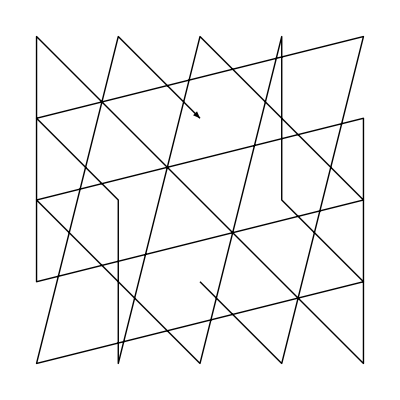
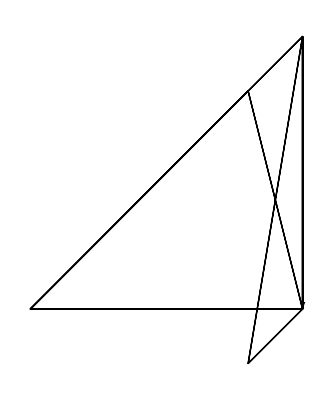
{(11 | 24 | 7 | 20 | 3
4 | 12 | 25 | 8 | 16
17 | 5 | 13 | 21 | 9
10 | 18 | 1 | 14 | 22
23 | 6 | 19 | 2 | 15),{-Graphics-,{{1,-1},{1,4},{-4,-1},{1,-1},{0,-2},{1,4},{1,-1},{1,-1},{-4,-1},{0,3},{1,-1},{1,-1},{1,-1},{1,-1},{0,3},{-4,-1},{1,-1},{1,-1},{1,4},{0,-2},{1,-1},{-4,-1},{1,4},{1,-1}},-Graphics-}}

```mathematica
GM[({{11, 24, 7, 20, 3}, {4, 12, 25, 8, 16}, {17, 5, 13, 21, 9}, {10, 18, 1, 14, 22}, {23, 6, 19, 2, 15}})]
```

```mathematica
Map[Piecewise[{{1, #>0}, {0, #==0}}]&,Normal[LatticeData["Leech","GeneratorMatrix"]]//MatrixForm,{3}]
```

```mathematica
ArrayPlot[({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 0, 0, 0, 0, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 1, 1, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 0, 1, 0, 1, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0}, {0, 1, 1, 1, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0}, {0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}})]
```

-Graphics-

```mathematica
LatticeData["Unimodular"]
```

{Leech,SimpleCubic,SquareLattice}

1:eJzFljEOgDAIRTHxEK7ex8kjOJh0cqj3j13blOY3H3Ah2KB9fqB0v57z3kQkr8UcKb/1U1qKkyTc9CjiUVQtQlHGGYlCAeoiAAWtTl+UqR5xQ1F7ZGz+1MJNFebUskOhz04TFKAu1L3tasVwjhDvAnOEWWO1sPFYClqGGRTn+wX4vamMNP8NbAHGoRlR5UYnzzAO7RFAHyAjWlxD0VMAvXMQaz0KwBifKwyFnYdmxNd8wUcuQw==

```mathematica
Map[FromDigits[#,2]&,Transpose[({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 0, 0, 0, 0, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 1, 1, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 0, 1, 0, 1, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0}, {0, 1, 1, 1, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0}, {0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}})]]
```

```mathematica
Reverse[{16777200,4264985,2167369,1118505,591737,328737,197137,65857,38783,21573,12835,4369,3855,1029,515,257,255,69,35,17,15,5,3,1}]
```

```mathematica
Table[{1,3,5,15,17,35,69,255,257,515,1029,3855,4369,12835,21573,38783,65857,197137,328737,591737,1118505,2167369,4264985,16777200}[[i+1]]-2^i,{i,0,23}]
```

```mathematica
Map[FactorInteger,{0,1,1,7,1,3,5,127,1,3,5,1807,273,4643,5189,6015,321,66065,66593,67449,69929,70217,70681,8388592}]//Column
```

```mathematica
{{{{0,1}}}, {{{1,1}}}, {{{1,1}}}, {{{PrimePi[7],1}}}, {{{1,1}}}, {{{PrimePi[3],1}}}, {{{PrimePi[5],1}}}, {{{PrimePi[127],1}}}, {{{1,1}}}, {{{PrimePi[3],1}}}, {{{PrimePi[5],1}}}, {{{PrimePi[13],1},{PrimePi[139],1}}}, {{{PrimePi[3],1},{PrimePi[7],1},{PrimePi[13],1}}}, {{{PrimePi[4643],1}}}, {{{PrimePi[5189],1}}}, {{{PrimePi[3],1},{PrimePi[5],1},{PrimePi[401],1}}}, {{{PrimePi[3],1},{PrimePi[107],1}}}, {{{PrimePi[5],1},{PrimePi[73],1},{PrimePi[181],1}}}, {{{PrimePi[66593],1}}}, {{{PrimePi[3],1},{PrimePi[22483],1}}}, {{{PrimePi[69929],1}}}, {{{PrimePi[7],2},{PrimePi[1433],1}}}, {{{PrimePi[13],1},{PrimePi[5437],1}}}, {{{PrimePi[2],4},{PrimePi[524287],1}}}}
```

{{0,1}}
{{1,1}}
{{1,1}}
{{4,1}}
{{1,1}}
{{2,1}}
{{3,1}}
{{31,1}}
{{1,1}}
{{2,1}}
{{3,1}}
{{6,1},{34,1}}
{{2,1},{4,1},{6,1}}
{{627,1}}
{{691,1}}
{{2,1},{3,1},{79,1}}
{{2,1},{28,1}}
{{3,1},{21,1},{42,1}}
{{6640,1}}
{{2,1},{2515,1}}
{{6930,1}}
{{4,2},{227,1}}
{{6,1},{718,1}}
{{1,4},{43390,1}}

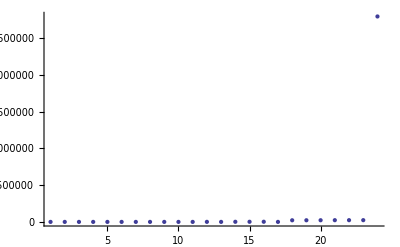

```mathematica
ListPlot[{0,1,1,7,1,3,5,127,1,3,5,1807,273,4643,5189,6015,321,66065,66593,67449,69929,70217,70681,8388592}]
```

```mathematica
FactorInteger[135151735692552575151029385543691283521573387836585719713732873759173711185052167369426498516777200]
```

$Aborted

```mathematica
PrimeQ[135151735692552575151029385543691283521573387836585719713732873759173711185052167369426498516777200]
```

PrimeQ::nonopt: Options expected (instead of 11185052167369426498516777200) beyond position 1 in PrimeQ[1351517356925525751510293855436912835215733878365857197137328737591737, 11185052167369426498516777200]. An option must be a rule or a list of rules.

PrimeQ[1351517356925525751510293855436912835215733878365857197137328737591737,11185052167369426498516777200]

```mathematica
(1705024+3992644)/64//N
```

89026.1

```mathematica
Table[{Prime[i],Divisible[135151735692552575151029385543691283521573387836585719713732873759173711185052167369426498516777200,Prime[i]]},{i,1,100}]
```

{{2,True},{3,False},{5,True},{7,False},{11,False},{13,False},{17,False},{19,False},{23,False},{29,False},{31,False},{37,False},{41,False},{43,False},{47,False},{53,False},{59,False},{61,False},{67,False},{71,False},{73,False},{79,False},{83,False},{89,False},{97,False},{101,False},{103,False},{107,False},{109,False},{113,False},{127,False},{131,False},{137,False},{139,False},{149,False},{151,False},{157,False},{163,False},{167,False},{173,False},{179,False},{181,False},{191,False},{193,False},{197,False},{199,False},{211,False},{223,False},{227,False},{229,False},{233,False},{239,False},{241,False},{251,False},{257,False},{263,False},{269,False},{271,False},{277,False},{281,False},{283,False},{293,False},{307,False},{311,False},{313,False},{317,False},{331,False},{337,False},{347,False},{349,False},{353,False},{359,False},{367,False},{373,False},{379,False},{383,False},{389,False},{397,False},{401,False},{409,False},{419,False},{421,False},{431,False},{433,False},{439,False},{443,False},{449,False},{457,False},{461,False},{463,False},{467,False},{479,False},{487,False},{491,False},{499,False},{503,False},{509,False},{521,False},{523,False},{541,False}}

```mathematica
135151735692552575151029385543691283521573387836585719713732873759173711185052167369426498516777200/(2^4*5^2)
```

337879339231381437877573463859228208803933469591464299284332184397934277962630418423566246291943

```mathematica
tf[x_]:=Piecewise[{{1, x==True}, {0, x==False}}]
```

```mathematica
Table[{Prime[i]*tf[Divisible[337879339231381437877573463859228208803933469591464299284332184397934277962630418423566246291943,Prime[i]]]},{i,101,200}]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{661},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
337879339231381437877573463859228208803933469591464299284332184397934277962630418423566246291943/661
```

511163902014192795578779824295352812108825218746542056405948841751791645934387924997830932363

```mathematica
Table[{Prime[i]*tf[Divisible[511163902014192795578779824295352812108825218746542056405948841751791645934387924997830932363,Prime[i]]]},{i,201,1000}]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{6449},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
511163902014192795578779824295352812108825218746542056405948841751791645934387924997830932363/6449
```

79262506127181391778381117118212561964463516629949148147921978872971258479514331678993787

```mathematica
DeleteDuplicates[Table[{Prime[i]*tf[Divisible[79262506127181391778381117118212561964463516629949148147921978872971258479514331678993787,Prime[i]]]},{i,300000,500000}]]
```

{{0},{4589633}}

```mathematica
79262506127181391778381117118212561964463516629949148147921978872971258479514331678993787/4589633
```

17269900692970743364094932452815412902178347730624463469720123346021622748379735739

```mathematica
Monitor[DeleteDuplicates[Table[{Prime[i]*tf[Divisible[17269900692970743364094932452815412902178347730624463469720123346021622748379735739,Prime[i]]]},{i,100000000,150000000}]],i]
```

```mathematica
p=Prime[100000000]
```

```mathematica
Do[Block[{p2=NextPrime[p]},p=p2;Block[{q=p2*tf[Divisible[17269900692970743364094932452815412902178347730624463469720123346021622748379735739,p2]]},Piecewise[{{0, q==0}, {Print[q], q>0}}]]],{i,1000000}]
```